## General Functions

This file was created with Mathematica/10.2 and can only be claimed to work (at most) on such a system. 

Prior to analysis you must :
(1) Run the simulations (see versatile_framework_paper/README.md)
(2) Postprocess: 
In most cases this means converting the human-readable-output of the simulation to something easier for mathematica to read. My solution was a “dat” file. The python script versatile_framework_paper/python/txt2dat.py converts the txt files from the simulation output to dat files that mathematica can import easily using the pts function, below.
Example Usage:
python versatile_framework_paper/python/txt2dat.py test actins
generates the file test/txt_stack/actins.dat from the file test/txt_stack/actins.txt. 
For Cytosim trajectories, there’s a similar command
python versatile_framework_paper/python/cs_txt2dat.py test 
to produce the “objects.dat” file
For most of the analyses below, this must be done for the links file and sometimes the actins file. 

For figures 2, 3D, 7C-D and S3 there are separate pre/post processing requirements; see there for details.

```mathematica
(*Import["~/Code/cytomod/analysis/cytomod_functions.m"];*)
```

### Directory Setup

```mathematica
outdir="/project/weare-dinner/simonfreedman/cytomod/out";
vfdir=outdir<>"/vf_r1";
figdir=vfdir<>"/figs";
fig1dir=outdir<>"/minimal_actomyosin/";
fig2dir=vfdir<>"/profiling/";
fig3dir=vfdir<>"/pl_small_ang/";
fig3Ddir="/scratch/midway2/simonfreedman/cytomod/out/vf_r1/pl_small_ang/L20_np100_tf100/";
fig5dir=vfdir<>"/shear/shear_xy75/kf1000/";
fig6dir=vfdir<>"/motility/lammps_bend";
fig7dir=vfdir<>"/contracting/xldens1";
figS2dir=vfdir<>"/shear/nbw_arr";
figS3dir=vfdir<>"/contracting/xldens1";

csoutdir="/project/weare-dinner/simonfreedman/cytosim/out";
figS4dir=csoutdir<>"/pl";
figS5dir=csoutdir<>"/motility";
```

### Reading Data

```mathematica
ClearAll[pts,pts3,readline,readline3];
pts[dir_,name_]:=
If[
FileExistsQ[dir<>"/txt_stack/"<>name<>".dat"],
ToExpression[Import[dir<>"/txt_stack/"<>name<>".dat","TSV"]],
Print[dir<>"/txt_stack/"<>name<>".dat doesn't exist"];{}
];
pts3[dir_,name_]:=Map[Internal`StringToDouble/@(StringSplit[StringTake[#,{2,-2}],", "])&,Import[dir<>"/txt_stack/"<>name<>".dat","TSV"],{2}];
readline[stream_,nrec_]:=ToExpression@Read[stream,ConstantArray["Record",nrec],RecordSeparators->{"\t","\n"}];
readline3[stream_,nrec_]:=Internal`StringToDouble/@(StringSplit[StringTake[#,{2,-2}],", "])&/@Read[stream,ConstantArray["Record",nrec],RecordSeparators->{"\t","\n"}];
ptsCS[dir_,name_]:=
If[
FileExistsQ[dir<>"/"<>name<>".dat"],
ToExpression[Import[dir<>"/"<>name<>".dat","TSV"]],
Print[dir<>"/"<>name<>".dat doesn't exist"];{}
];
```

### Drawing Networks

```mathematica
ClearAll[link,actin,amotor,pmotor,draw,drawStretch];
link[l_,maxLength_:100,color_:Red]:=Graphics[
{color,
Thick,
If[Norm[l[[3;;4]]]<maxLength,
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}],
Point[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
]
}
];
actin[a_,col_]:=Graphics[
{col,
Disk[{a[[1]],a[[2]]},a[[3]]]
}
];
radactin[a_,col_,rad_]:=Graphics[
{col,
Disk[{a[[1]],a[[2]]},rad]
}
];

amotor[l_,maxLength_:2]:=Graphics[
{Black,
Thickness[0.025],
If[Norm[l[[3;;4]]]<maxLength,
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}],
Point[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
]
}
];
pmotor[l_,col_:Yellow]:=Graphics[
{col,
Opacity[1],
Thickness[0.02],
(*Arrowheads[{-0.005,0.005}],*)
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];

draw[actins_,links_,amotors_,pmotors_,dir_:"",movieFlag_:False,fov_: {500,500},dt_: 1,polar_: True,np_: 11,acolor_: Red,movieName_: "movie",maxLinkLength_:-1,barbedEndFactor_: 3]:=Module[{},(*Generate Image Time Series,make into movie*)
mll=If[maxLinkLength==-1,Abs[Min[fov]/2],maxLinkLength];
frames={};
If[actins≠{},AppendTo[frames,Map[actin[#,acolor]&,actins,{2}]]];
If[links≠{},AppendTo[frames,Map[link[#,mll]&,links,{2}]]];
If[polar,
If[actins≠{},AppendTo[frames,Map[actin[#,Blue]&,actins[[All,1;;-1;;np]],{2}]],If[links≠{},rad=Mean[Flatten[Map[Norm,links[[All,All,3;;4]],{2}]]]/barbedEndFactor;
AppendTo[frames,Map[radactin[#,Lighter[Blue],rad]&,links[[All,1;;-1;;np-1]],{2}]]]]];
If[amotors≠{},AppendTo[frames,Map[amotor,amotors,{2}]]];
If[pmotors≠{},AppendTo[frames,Map[pmotor[#,Green]&,pmotors,{2}]]];
frames=Transpose[frames];
minx=0;miny=0;maxx=0;maxy=0;
If[TensorRank[fov]==1,minx=-fov[[1]]/2;maxx=fov[[1]]/2;miny=-fov[[2]]/2;
maxy=fov[[2]]/2,minx=fov[[1,1]];maxx=fov[[1,2]];miny=fov[[2,1]];
maxy=fov[[2,2]]];
frames=Map[Show[#,Frame->True,PlotRange->{{minx,maxx},{miny,maxy}},(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)FrameTicks->None,Ticks->None,BaseStyle->{FontSize->24,FontColor->Black}]&,frames];
If[movieFlag,Export[dir<>"/data/"<>movieName<>".avi",frames]];
frames];

drawStretch[actins_,links_,amotors_,pmotors_,dir_,movieFlag_,fov_:{500,500},dt_:1,acolor_:Red,cell_:{0,0},strainPct_:0,l0_:1,
colorByEnergy_:True,enghilo_:{0,0},scheme_:"BlueGreenYellow",bgcol_:White]:=
Module[
{actinsr=actins, linksr=links,amotorsr=amotors,pmotorsr=pmotors},
(*Generate Image Time Series, make into movie*)
δrx=strainPct*fov[[1]]*cell[[2]];
cm=fov*cell;
minx=fov[[1]](cell[[1]]-0.5);
maxx=fov[[1]](cell[[1]]+0.5);
miny=fov[[2]](cell[[2]]-0.5);
maxy=fov[[2]](cell[[2]]+0.5);
frames={};
If[colorByEnergy,
If[enghilo[[1]]==enghilo[[2]],
engs=(Norm/@Flatten[links[[All,All,3;;4]],1]-l0);
cf=ColorData[{scheme,{Min[engs],Max[engs]}}],
cf=ColorData[{scheme,{enghilo[[1]],enghilo[[2]]}}]
],
cf[i_]:="Red"
];
If[actinsr≠{},
actinsr[[All,All,1;;2]]=Map[ (#+cm+{δrx,0})&,actinsr[[All,All,1;;2]],{2}];AppendTo[frames,Map[actin[#,Blend[{acolor,Red},Part[#,5]/10.]]&,actinsr,{2}]]];
If[linksr≠{},
linksr[[All,All,1;;2]]=Map[ (#+cm+{δrx,0})&,linksr[[All,All,1;;2]],{2}];
AppendTo[frames,Map[link[#,Abs[0.5fov[[1]]],cf[Abs[Norm[#[[3;;4]]]-l0]]]&,linksr,{2}]]
];
If[amotorsr≠{},
amotorsr[[All,All,1;;2]]=Map[(#+cm+{δrx,0})&,amotorsr[[All,All,1;;2]],{2}];
AppendTo[frames,Map[amotor,amotorsr,{2}]]];
If[pmotorsr≠{},
pmotorsr[[All,All,1;;2]]=Map[(#+cm+{δrx,0})&,pmotorsr[[All,All,1;;2]],{2}];AppendTo[frames,Map[pmotor,pmotorsr,{2}]]];
frames=Transpose[frames];
frames=Map[
Show[#,
Frame->True,
PlotRange->{{minx,maxx},{miny,maxy}},
Background->bgcol,
(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)
FrameTicks->None,
Ticks->None,
BaseStyle->{FontSize->24,FontColor->Black}
]&
,frames
];
If[movieFlag, Export[dir<>"/data/movie_"<>ToString[scheme]<>".avi",frames]];
frames
];
```

### Plotting Options

```mathematica
Needs["CustomTicks`"] (*Get this package, it's great!*)
```

```mathematica
SetOptions[{Plot,LogLogPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot},BaseStyle->{FontFamily->"Arial",FontSize->22,SingleLetterItalics->False},Frame->True,AspectRatio->0.8,FrameStyle->Black];
SetOptions[{ListVectorPlot,ListVectorDensityPlot,VectorPlot},BaseStyle->{FontSize->26,FontFamily->"Arial"},
FrameStyle->Black,VectorStyle->Black];
SetOptions[{ListDensityPlot,DensityPlot},BaseStyle->{FontSize->26,FontFamily->"Arial"},
FrameStyle->Black];
```

### Periodic Boundary Conditions

```mathematica
rijP[dr_,fov_]:=dr-Round[dr/fov]*fov;
```

### Persistence Length Calculations

```mathematica
ClearAll[anglesT, anglesBwT, ccf,th2];
anglesT[rt_]:=ArcTan[rt[[All,3]],rt[[All,4]]];
anglesTCS[rt_]:=ArcTan[rt[[All,1]],rt[[All,2]]];
anglesBwT[angs_]:=Map[(#-2Pi Floor[#/(2Pi)+0.5])&,angs[[2;;]]-angs[[1;;-2]]];
ccf[ths_]:=Module[{},
sums=Table[Accumulate[ths[[i;;]]],{i,Length[ths]}];
Table[Mean[Cos[sums[[1;;Length[sums]-i,i+1]]]],{i,0,Length[sums]-1}]
];
th2[ths_]:=Module[{},
sums=Table[Accumulate[ths[[i;;]]],{i,Length[ths]}];
Table[Mean[sums[[1;;Length[sums]-i,i+1]]^2],{i,0,Length[sums]-1}]
];
plMeanThsq[drs_,dx_,L_,maxL_]:=Module[{},
angs=ArcTan[drs[[All,All,1]],drs[[All,All,2]]];
angsbw=anglesBwT/@angs;
th2s=th2/@angsbw;
muths=Mean[th2s];
dat={Range[dx,L-dx,dx],muths}ᵀ;
fit=LinearModelFit[dat[[1;;Min[maxl,Length[dat]]]],x,x];
lp=1/D[Normal[fit],x];
ClearAll[angs,angsbw,th2s,muths,dat,fit];
lp
];
plThsq[drs_,maxX_]:=Module[{},
angs=ArcTan[drs[[All,1]],drs[[All,2]]];
angsbwt=anglesBwT[angs];
th2s=th2[angsbwt];
dx=Mean[Norm/@drs];
dat={Range[dx,maxX dx-dx,dx],th2s[[1;;(maxX-1)]]}ᵀ;
fit=LinearModelFit[dat,x,x];
lp=1/D[Normal[fit],x];
ClearAll[angs,angsbwt,th2s,dx,dat,fit];
lp
]
```

### Radial Distribution Function

```mathematica
rdf[acts_,fov_,δr_,maxr_,sampPairs_]:=Module[{},
rs=Range[0,maxr,δr];
rsmid=(rs[[2;;]]+rs[[;;-2]])0.5;
norms=2Pi δr rsmid Length[sampPairs]/(fov[[1]]*fov[[2]]);
rdft=
Table[
BinCounts[
Map[
Norm[rijP[#,fov]]&,
acts[[t,sampPairs[[All,1]],1;;2]]-acts[[t,sampPairs[[All,2]],1;;2]]],
{0,maxr,δr}]/norms,
{t,Length[acts]}
];
rdft
];
```

### Filament Strain

```mathematica
ClearAll[filstrain];
filstrain[acts_,fov_:{50,50},nparts_:500]:=
Map[
Norm[
rijP[#,fov]]&,
acts[[All,Length[acts[[1]]]/nparts;;-1;;Length[acts[[1]]]/nparts,1;;2]]-acts[[All,1;;-1;;Length[acts[[1]]]/nparts,
1;;2]],
{2}];
```

### Gaussian Radial Basis Function Interpolation

```mathematica
ClearAll[velx,vely,div];
velx[x_,y_,vf_]:=vf[[All,3]].Exp[(-1./vf[[All,5]]^2)*((Total[#^2]&)/@Transpose[{x,y}-{vf[[All,1]],vf[[All,2]]}])];
vely[x_,y_,vf_]:=vf[[All,4]].Exp[(-1./vf[[All,5]]^2)*((Total[#^2]&)/@Transpose[{x,y}-{vf[[All,1]],vf[[All,2]]}])];
div[x_,y_,vf_]:=(-2/vf[[All,5]]^2(vf[[All,3]](x-vf[[All,1]])+vf[[All,4]](y-vf[[All,2]]))).Exp[(-1./vf[[All,5]]^2)*((Total[#^2]&)/@Transpose[{x,y}-{vf[[All,1]],vf[[All,2]]}])];
```

### Mean Squared Displacement

```mathematica
ClearAll[mdsp,msdpc]
ClearAll[msdp]
msdp[drs_]:=Module[{},
sums=Table[Accumulate[drs[[t;;]]],{t,Length[drs]}];
dx2s=sums[[All,All,1]]^2+sums[[All,All,2]]^2;
msd=Table[Mean[dx2s[[1;;-t,t]]],{t,1,Length[dx2s]}];
ClearAll[sums,dx2s];
msd
];
msdpc:=Compile[{{drs,_Real,2}},
sums=Table[Accumulate[drs[[t;;-1]]],{t,1,Round[Length[drs]]}];
dx2s=sums[[All,All,1]]^2+sums[[All,All,2]]^2;
msd=Table[Mean[dx2s[[1;;-t,t]]],{t,1,Length[dx2s]}];
ClearAll[sums,dx2s];
msd,
{{t,_Integer}}
];
```

## Figure 1

### D

Requires first running 
	txt2dat.py [fig1dir <> "/slide/"] links
	txt2dat.py [fig1dir <> "/slide/"] amotors

```mathematica
dir=fig1dir<>"/slide";
lks=pts[dir,"links"];
amots=pts[dir,"amotors"];
fs=draw[{},lks,amots,{},dir,False,{20,5},1,True, 21,Red,"movie",-1,1];
GraphicsColumn[fs[[{1,31,101}]],Spacings->10]
```

### E

Requires first running 
	txt2dat.py [fig1dir <> "/buckle/"] links
	txt2dat.py [fig1dir <> "/buckle/"] amotors
	txt2dat.py [fig1dir <> “/buckle/”] pmotors

```mathematica
dir=fig1dir<>"/buckle";
lks=pts[dir,"links"];
amots=pts[dir,"amotors"];
pmots=pts[dir,"pmotors"];
fs=draw[{},lks,amots,pmots,dir,False,{20,5},1,True, 21,Red,"movie",-1,1];
GraphicsColumn[fs[[{1,31,101}]],Spacings->10]
```

## Figure 2

For these plots, you have to measure the wall clock time of the simulation. I did this with the following Bash script, where $cmd was my simulation command (see versatile_framework_paper/README.md) and $data_dr was the “data” output directory of the simulation

startt = `date + % s`
./$cmd
endt = `date + % s`
tott = $ (echo $startt $endt | awk' {printf "%d", $2 - $1}')
echo $tott > "$data_dr/time.txt"

### A

```mathematica
nfil0=20;
nm0=11;
ρ0=0.1;
area=50^2;
```

#### Red Curve

```mathematica
dir=fig2dir<>"/2A/npoly_arr";
ns=Sort[Flatten[Outer[Times,{1,2,5},10^Range[0,3]]]];
dirs=Table[dir<>"/dens"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=ns nm0+4ρ0 area;(*in paper, constant addition was off -- 4*0.1*75^2"*)
reddat={nparts,times}ᵀ;
```

#### Blue Curve

```mathematica
dir=fig2dir<>"/2A/mdens_arr";
ns=Sort[Flatten[Outer[Times,{1,2,5},10^Range[0,4]]]];
denss=ns*0.001;
dirs=Table[dir<>"/dens"<>ToString[NumberForm[d,{3,3}]],{d,denss}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=nfil0 nm0+2ρ0 area + 2 denss area;
bluedat={nparts,times}ᵀ;
```

#### Black Curve

```mathematica
dir=fig2dir<>"/2A/dens_arr";
ns=Sort[Flatten[Outer[Times,{1,2,5},10^Range[0,3]]]];
dirs=Table[dir<>"/dens"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
nparts=ns nm0+4 ρ0 ns/nfil0 area;
blackdat={nparts,times}ᵀ;
```

```mathematica
ticksb=LogTicks[10,2,6];
tickst=LogTicks[10,2,6,ShowTickLabels->False];
ticksl=LogTicks[10,0,10];
ticksr=LogTicks[10,0,10,ShowTickLabels->False];
```

```mathematica
npartplt=Show[
ListPlot[
{Log10[reddat[[4;;]]],Log10[bluedat[[6;;]]],Log10[blackdat[[4;;]]]},
PlotMarkers->{●,10},PlotStyle->{Red,Blue,Black},Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,tickst}},
PlotRange->{{2.7,5.55},{0,5.2}},FrameLabel->{"# Particles","Wall Clock Time (s)"},
PlotLegends->Placed[PointLegend[{"ρ_motor const.","ρ_actin const."},LabelStyle->FontSize->18,LegendMarkerSize->{30,30},Spacings->0.1],{0.7,0.2}]],
Plot[{x-2.3,2x-4.7},{x,1,7},PlotStyle->{{Blue,Thick,Dashed},{Black,Thick,Dashed}}]];
```

```mathematica
npartplt
```

```mathematica
Export[figdir<>"2A.eps",npartplt];
```

### B

```mathematica
dir=fig2dir<>"/sys_size_arr";
ns=10Range[10];
dirs=Table[dir<>"/sz"<>ToString[n],{n,ns}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
szs=ns^2;
blackdat={szs,times}ᵀ;
```

```mathematica
ticksb=LogTicks[10,1,4,TickLabelStep->0.25];
tickst=LogTicks[10,1,4,ShowTickLabels->False];
ticksl=LogTicks[10,0,4];
ticksr=LogTicks[10,0,4,ShowTickLabels->False];
szplt=Show[ListPlot[Log10[blackdat],PlotMarkers->{●,10},Axes->False,
PlotStyle->Black,Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,tickst}},
PlotRange->{Automatic,{1,4}},
FrameLabel->{"System Size (μm^2)","Wall Clock Time (s)"}],
Plot[{x-0.1},{x,2,5},PlotStyle->{{Blue,Thick,Dashed},{Red,Thick,Dashed}}]]
```

```mathematica
Export[figdir<>"/2B.eps",szplt];
```

### C

```mathematica
dir=fig2dir<>"/grid_factor/";
ns=Join[{9},10Range[10],{200}];
gfs=ns*0.01;
dirs=Table[dir<>"gf"<>ToString[NumberForm[gf,{1,2}]],{gf,gfs}];
times=Flatten[Table[Import[dr<>"/data/time.txt","TSV"],{dr,dirs}]];
blackdat={gfs,times}ᵀ;
```

```mathematica
ticksb=LogTicks[10,-2,0,TickLabelStep->0.25];
tickst=LogTicks[10,-2,0,ShowTickLabels->False];
ticksl=LogTicks[10,3,6];
ticksr=LogTicks[10,3,6,ShowTickLabels->False];
gfplt=Show[ListPlot[Log10[blackdat],PlotMarkers->{●,10},Axes->False,
PlotStyle->Black,Joined->True,
FrameTicks->{{ticksl,ticksr},{ticksb,tickst}},
PlotRange->Full,
FrameLabel->{"Grid Density (μm^-1)","Wall Clock Time (s)"}],
Plot[{-2x+3,-x+4.25},{x,-2,1},PlotStyle->{{Red,Thick,Dashed},{Blue,Thick,Dashed}}]]
```

```mathematica
Export[figdir<>"/2C.eps",gfplt];
```

## Figures 3, S1

### 3 B

```mathematica
dx=1;
L=20;
nfils=20;
nlks=L/dx;
teq=100;
lp=17;
```

```mathematica
fig3Adir=fig3dir<>"/x1/kl_arr_pl17/kl1.00";
lks=Partition[#,nlks]&/@pts[fig3Adir,"links"];
angs=ParallelMap[anglesT,lks,{2}];
angsbw=ParallelMap[anglesBwT,angs,{2}];
ccfs=ParallelMap[ccf,angsbw,{2}];
th2s=ParallelMap[th2,angsbw,{2}];
```

```mathematica
muths=Mean[th2s[[teq;;]]];
muthsmu=Mean[muths];
muthserr=StandardDeviation[muths]/Sqrt[Length[muths]];
```

```mathematica
muccfs=Mean[ccfs[[teq;;]]];
muccfsmu=Mean[muccfs];
muccfserr=StandardDeviation[muccfs]/Sqrt[Length[muccfs]];
```

```mathematica
xs=Range[dx,L-dx,dx];
```

```mathematica
th2plt=Show[
ListPlot[{
{xs,muthsmu}ᵀ,
{xs,muthsmu-muthserr}ᵀ,
{xs,muthsmu+muthserr}ᵀ},
FrameLabel->{"","","",Rotate[Style["⟨θ^2(ℓ)⟩",Blue],Pi]},
FrameStyle->Blue,
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Blue,{Blue,Opacity[0.01]},{Blue,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},*)
(**)
(*Uncomment next four line if you don't want joined*)

FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Blue,
Joined->False,

Filling->{2->{3}},
PlotRange->{{0,20},Automatic}
],
Plot[{x/(lp)},{x,0,50},PlotStyle->{Thick,Dashing[Large],Blue}]
];
```

```mathematica
ccfplt=Show[
ListLogPlot[{
{xs,muccfsmu}ᵀ,
{xs,muccfsmu-muccfserr}ᵀ,
{xs,muccfsmu+muccfserr}ᵀ},
FrameLabel->{"ℓ (μm)",Style["⟨cosθ(ℓ)⟩",Red]},
FrameStyle->{{Red,Automatic},{Black,Black}},
Frame->{{True,False},{True,True}},
FrameTicks->{{All,None},{All,Automatic}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Red,{Red,Opacity[0.01]},{Red,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},
*)(**)
(*Uncomment next four line if you don't want joined*)
(**)
FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Red,
Joined->False,
(**)
Filling->{2->{3}},
PlotRange->{{0,20},Automatic}],
LogPlot[{Exp[-x/(2lp)]},{x,0,50},PlotStyle->{Thick,Dashing[Large],Red}]
];
```

```mathematica
GraphicsRow[{ccfplt,th2plt}]
```

```mathematica
Export[figdir<>"/3BRed_stderr_joined.eps",ccfplt];
Export[figdir<>"/3BBlue_stderr_joined.eps",th2plt];
```

### S1

```mathematica
dir=fig3dir<>"/x1/decor";
lks=pts[dir,"links"];
angs=anglesT/@lks;
angsbw=anglesBwT/@angs;
ccs=Table[CorrelationFunction[angsbw[[All,i]],{0,19999}],{i,1,Length[angsbw[[1]]]}];
mccs=Mean[ccs];
cf={0.005(Range[Length[mccs]]-1),mccs}ᵀ;
decortimes=0.01Table[Total[mccs[[1;;i]]],{i,2,20000}];
```

#### S1A

```mathematica
ps=Join[Range[1,5],Range[7,15,2],Range[20,100,20],Range[150,2000,50]];
```

```mathematica
plta=Show[ListLogPlot[cf,PlotRange->{{-0.1,10.1},{0.005,1.2}},Joined->True,PlotStyle->Black,FrameLabel->{"s  (sec)",Style["R(θ,s)",SingleLetterItalics->False]}],
ListLogPlot[cf[[ps]],PlotRange->Full,PlotMarkers->{●,7},PlotStyle->Black]]
```

```mathematica
Export[figdir<>"/S1A.eps",plta];
```

#### S1B

```mathematica
pltb=ListPlot[decortimes, PlotRange->{{0,10},{0,1.05}},PlotStyle->{Black,Thick},DataRange->{0,100},FrameLabel->{"t_final (sec)","τ (sec)"}]
```

```mathematica
Export[figdir<>"/S1B.eps",pltb];
```

### 3 D

```mathematica
seeds=Range[1,1000];
dirs=Table[fig3Ddir<>"seed"<>ToString[s],{s,seeds}];
nfils=100;
tf=2001;
```

#### Evaluate the eigenvalues for the first time

```mathematica
fstreams=OpenRead[#<>"/txt_stack/actins_ext.dat"]&/@dirs;
evs={};
Do[
actsextt=Table[readline3[f,2*nfils],{f,fstreams}];
AppendTo[evs,Table[Eigenvalues[Covariance[actsextt[[All,i,1;;2]]]],{i,2*nfils}]];,
{tf}
];
Export[fig3Ddir<>"/all_evs.dat",evs];
```

#### Import Previously evaluated eigenvalues

```mathematica
evs=ToExpression[Import[fig3Ddir<>"/all_evs.dat","TSV"]];
```

```mathematica
ts=Range[0.001,tf*0.001,0.001];
maxevs=evs[[All,All,1]];
minevs=evs[[All,All,2]];
mumaxevs=Mean/@maxevs;
muminevs=Mean/@minevs;
errmaxevs=(StandardDeviation/@maxevs)/Sqrt[Dimensions[evs][[2]]];
errminevs=(StandardDeviation/@minevs)/Sqrt[Dimensions[evs][[2]]];
```

```mathematica
maxmaxevs=Max/@maxevs;
maxminevs=Max/@minevs;
minmaxevs=Min/@maxevs;
minminevs=Min/@minevs;
```

```mathematica
maxnorm=mumaxevs[[1000]];
minnorm=muminevs[[1000]];
```

```mathematica
idxs=Union[Round[10^Range[Log10[2],Log10[2000],0.05]]];
```

```mathematica
ticksx=LogTicks[10,-3,1];
fluctplt=Show[
ListPlot[Log10[{
{ts,mumaxevs/maxnorm}ᵀ[[idxs]],
{ts,(mumaxevs-errmaxevs)/maxnorm}ᵀ[[idxs]],
{ts,(mumaxevs+errmaxevs)/maxnorm}ᵀ[[idxs]],
{ts,muminevs/minnorm}ᵀ[[idxs]],
{ts,(muminevs-errminevs)/minnorm}ᵀ[[idxs]],
{ts,(muminevs+errminevs)/minnorm}ᵀ[[idxs]]
}],
PlotRange->{{-2.5,Log10[1.2]},{-2.5,0.8}},
PlotStyle->{Blue,{Blue,Opacity[0.1]},{Blue,Opacity[0.1]},Red,{Red,Opacity[0.1]},{Red,Opacity[0.1]}},
PlotMarkers->{{●,7},{○,0.01},{○,0.01},{●,7},{○,0.01},{○,0.01}},
Filling->{2->{3},5->{6}},
FrameLabel->{"t (s)","λ(t)/λ(1)"},
FrameTicks->{{ticksx,Automatic},{ticksx,Automatic}},Joined->{False,True,True,False,True,True},Axes->None
],
LogLogPlot[{t^{7/8},1.05t^{0.75}},{t,0.001,10},PlotStyle->{{Blue,Thick,Dashed},{Red,Thick,Dashed}}]
];
```

```mathematica
fluctplt
```

```mathematica
Export[figdir<>"/3C.eps",fluctplt];
```

## Figure 4

```mathematica
nlks=20;
dx=1;
L=20;
teq=100;
nfils=20;
teq=100;
Lp=17;
maxl=5;

ticksx=LogTicks[10,-3,3];
rngy={15.9,18.1};
```

### A

```mathematica
kbdir=fig3dir<>"/x1_kl1/kb_arr";
kbs={0.005,0.01,0.02,0.05,0.1,0.2,0.5,1.0,2.0,5,10,20,50,100,200,500};
kbdirs=kbdir<>"/kb"<>ToString[NumberForm[#,{1,3},ExponentFunction->(Null&)]]&/@kbs;
```

```mathematica
lks=ParallelTable[Partition[#,nlks]&/@(pts[kbdirs[[i]],"links"][[teq;;-2]]),{i,Length[kbs]}];
lps=ParallelTable[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dx,L,maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
lplpplt=Show[
ListLogLogPlot[
{{kbs/0.004,lpmeans}ᵀ(*,
{kbs/0.004,lpmeans-lperrs}ᵀ,
{kbs/0.004,lpmeans+lperrs}ᵀ*)
},
PlotMarkers->{{●,10},"+","+"},
PlotStyle->{Black,Red,Red},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]]
],
LogLogPlot[x,{x,0.1,100000},PlotStyle->{Black,Dashing[0.02](*,Thick*)}],
FrameLabel->{"κ_B (k_BT×μm)","L_p(μm)"}];
```

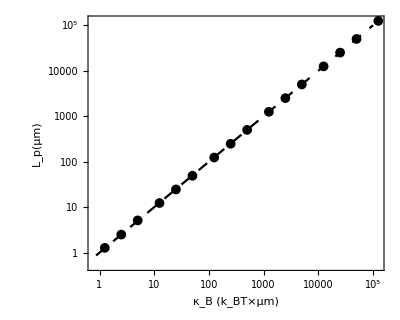

```mathematica
lplpplt
```

```mathematica
Export[figdir<>"/4A.eps",lplpplt];
```

### B

```mathematica
kldir=fig3dir<>"/x1/kl_arr_pl17/";
kls={0.01,0.02,0.05,0.1,0.2,0.5,1.0,2,5,10,20,50,100,200,500,1000};
kldirs=kldir<>"/kl"<>ToString[NumberForm[#,{2,2},ExponentFunction->(Null&)]]&/@kls;
```

```mathematica
lks=ParallelTable[Partition[#,nlks]&/@(pts[kldirs[[i]],"links"][[teq;;]]),{i,Length[kls]}];
lps=ParallelTable[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dx,L,maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
kllpplt=Show[
ListPlot[
{{Log10[kls],lpmeans}ᵀ,
{Log10[kls],lpmeans-lperrs}ᵀ,
{Log10[kls],lpmeans+lperrs}ᵀ
},
PlotMarkers->{{●,10},"+","+"},
PlotStyle->{Black,Red,Red},
PlotRange->{Automatic,rngy},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]],
Axes->False,
FrameTicks->{{Automatic,Automatic},{ticksx,Automatic}}
],
Plot[Lp,{x,-3,4},PlotStyle->{Black,Dashing[0.02](*,Thick*)}],
FrameLabel->{"k_a (pN/μm)","L_p(μm)"}];
```

```mathematica
kllpplt
```

```mathematica
Export[figdir<>"/4B.eps",kllpplt];
```

### C

```mathematica
dxdir=vfdir<>"/pl_small_ang/x1_nm21_lp17/dx_arr_kldx1/";
dxs={0.08,0.1,0.2,0.25,0.4,0.5,0.8,1,2,2.5,5};
Ls=nlks*dxs;
dxdirs=dxdir<>"/dx"<>ToString[NumberForm[#,{2,2},ExponentFunction->(Null&)]]&/@dxs;
```

```mathematica
lks=ParallelTable[Partition[#,nlks]&/@(pts[dxdirs[[i]],"links"][[teq;;-2]]),{i,Length[dxs]}];
lps=ParallelTable[Table[plMeanThsq[lks[[i,All,j,All,3;;4]],dxs[[i]],Ls[[i]],maxl],{j,Length[lks[[i,1]]]}],{i,Length[lks]}];;
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
dxlpplt=Show[
ListLogLinearPlot[
{{dxs,lpmeans}ᵀ,
{dxs,lpmeans-lperrs}ᵀ,
{dxs,lpmeans+lperrs}ᵀ
},
PlotMarkers->{{●,10},"+","+"},
PlotStyle->{Black,Red,Red},
PlotRange->{{0.07,1.2},rngy},
Joined->False,
Filling->{{2->{3}},{5->{6}}},
FillingStyle->Directive[Opacity[1],Thickness[0.01]]
],
LogLinearPlot[Lp,{x,0.001,10000},PlotStyle->{Black,Dashing[0.02]}],
FrameLabel->{"l_a (μm)","L_p(μm)"}];
```

```mathematica
dxlpplt
```

```mathematica
Export[figdir<>"/4C.eps",kllpplt];
```

## Figures 5, S2, S6

### A

```mathematica
dir=fig5dir<>"/kcl20.0";
γs=Range[0.001,0.5,0.001];
lks=pts[dir,"links"];
s=0.5;
boxsz=75;
fov=boxsz{1,1};
pr=boxsz*{{-0.5,0.5},{-0.5,0.5}};
engs=(Norm/@Flatten[lks[[All,All,3;;4]],1]-1);
englims={-0.025,0.025};
```

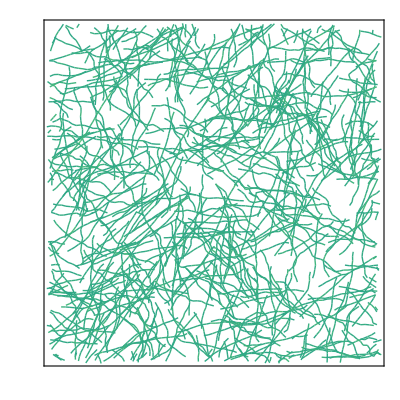
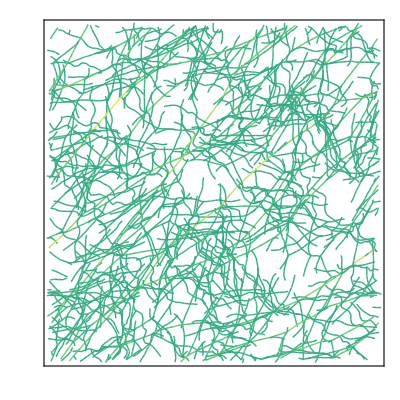
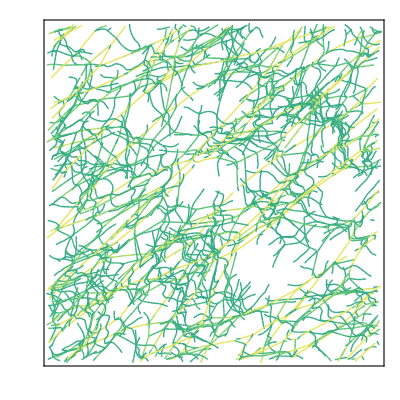

```mathematica
fs0=drawStretch[{},{lks[[21]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
fs1=drawStretch[{},{lks[[51]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
fs2=drawStretch[{},{lks[[-1]]},{},{},"",False,fov,1,Red,{0,0},s,1,True,englims];
{fs0,fs1,fs2}
```

```mathematica
Export[figdir<>"/5Atop.eps",Show[fs0]];
Export[figdir<>"/5Amid.eps",Show[fs1]];
Export[figdir<>"/5Abot.eps",Show[fs2]];
```

### B

```mathematica
strain=Flatten[Table[ConstantArray[0.001*i,20],{i,1,500}]];
te=Total[Transpose[Import[dir<>"/data/pe.txt","TSV"]]];
rng0=Range[1,101];
rng0b=Range[1,101,5];
rng1=Range[2000,2100,5];
rng2=Range[5000,5100,5];
rng3=Range[8000,8100,5];
ClearAll[tickfcn];
tickfcn[min_,max_,nticks_:50,nlabels_:5]:=Table[{x,If[Mod[x nlabels/(max-min),1]==0,ToString[N[x]],""]},{x,min,max,(max-min)/(nticks)}]
ts=Range[0,0.49999,0.5/10000];
p1=ListPlot[{ts[[rng0b]],te[[rng1]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{●,10},
FrameTicks->{{None,{44,46}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameStyle->{Thick,Blue}];
p2=ListPlot[{ts[[rng0b]],te[[rng2]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{■,10},
FrameTicks->{{None,{360,370,380}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameLabel->{"","","",Style[Rotate["U_tot (pNμm)",Pi],Blue]},
FrameStyle->{Thick,Blue}];
p3=ListPlot[{ts[[rng0b]],te[[rng3]]}ᵀ,
Joined->True,
PlotRange->Automatic,
PlotStyle->Blue,
PlotMarkers->{▲,10},
FrameTicks->{{None,{1975,2025}},{None,None}},
Frame->{{False,True},{False,False}},
ImageSize->350,AspectRatio->0.8/3,
FrameStyle->{Thick,Blue}];
strplt=ListPlot[{ts[[rng0]]*1000,strain[[rng0]]}ᵀ,Joined->True,PlotStyle->{Black,Dashed,Thick},BaseStyle->FontSize->22,
FrameTicks->{{tickfcn[0.000,0.006,30,6],None},{(*tickfcn[0,10,50,5]*)All,Automatic}},FrameLabel->{Style["t-t_0(ms)",SingleLetterItalics->False],"γ-γ_0","",""},
FrameStyle->{{Black,{Blue,Dashing[0.01]}},{Black,Black}},
AspectRatio->1,
Frame->{{True,True},{True,True}},
ImagePadding->{{Automatic,100},{Automatic,Automatic}},
ImageSize->400];
```

```mathematica
Manipulate[
Overlay[{
Overlay[{
Overlay[{strplt,
Show[p1,ImageSize->s1]},Alignment->{x1,y1}],
Show[p2,ImageSize->s2]},Alignment->{x2,y2}],
Show[p3,ImageSize->s3]},Alignment->{x3,y3}],
{s1,100,400},{x1,-1,1},{y1,-1,1},
{s2,100,400},{x2,-1,1},{y2,-1,1},
{s3,100,400},{x3,-1,1},{y3,-1,1}
]
```

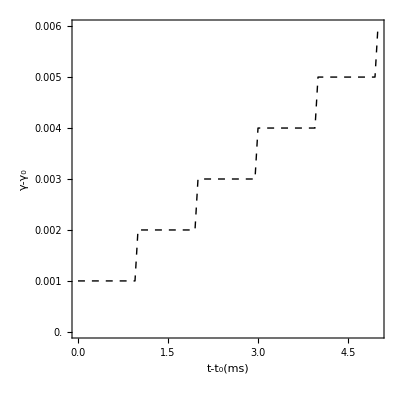
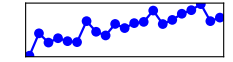
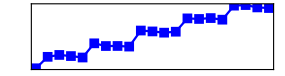
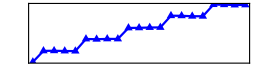

```mathematica
plt=Overlay[{
Overlay[{
Overlay[{strplt,
Show[p1,ImageSize->s1]},Alignment->{x1,y1}],
Show[p2,ImageSize->s2]},Alignment->{x2,y2}],
Show[p3,ImageSize->s3]},Alignment->{x3,y3}]/.{
s1->233,s2->285,s3->260,
x1->0.165,x2->0.63,x3->0.385,
y1->-0.51,y2->0.2,y3->0.755}
```

```mathematica
Export[figdir<>"/5B.png",plt];
```

```mathematica
Export[figdir<>"/5Bleft.eps",strplt];
Export[figdir<>"/5Bbot.eps",p1];
Export[figdir<>"/5Bmid.eps",p2];
Export[figdir<>"/5Btop.eps",p3];
```

### C

```mathematica
kls={0.1,0.2,0.5,1,2,5,10,20,50,100,200,500,1000};
dirs=fig5dir<>"/kcl"<>ToString[NumberForm[#,{2,1}]]&/@kls;
dt=10^(-6);
tfs=0.5;
engs=Transpose/@Table[Import[dr<>"/data/pe.txt","TSV"],{dr,dirs}];
te=Total/@engs;
ts=Range[0,0.49999,0.5/10000];
γs=Range[1,500]0.001;
eqengs=Table[Mean/@Partition[te[[i]],20],{i,Length[te]}];
ClearAll[myplt];
myplt[dat_,title_,legtitle_,x10offset_:0,x15offset_:0,lgdIdxs_:All]:=
Show[
ListLogLogPlot[dat,
PlotStyle->"BlueGreenYellow",
Frame->True,
FrameStyle->Black,
FrameLabel->{"γ","w (pN/μm)",title}
],
Plot[{2x+x10offset,7/2x+x15offset},{x,-4,10},PlotStyle->{{Darker[Blue],Dashed,Thick},{Darker[Green],Dashed,Thick}}],
BaseStyle->{FontFamily->"Arial",FontSize->22},
AspectRatio->0.8
];
dats=({γs[[1;;Length[#]]],#/75^2}ᵀ)&/@eqengs;
```

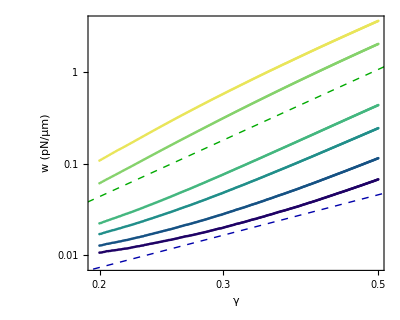

```mathematica
idxs={4,5,6,7,10,13};
plt=myplt[dats[[idxs,200;;]],"","k_cl [pN/μm]",-1.7,2.5,idxs]
```

```mathematica
Export[figdir<>"/5C.eps",plt];
```

### D (continued from C)

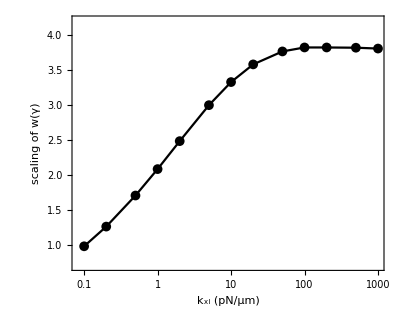

```mathematica
fs=Fit[#,{1,x},x]&/@Log[dats[[1;;,200;;]]];
exps=D[fs,x];
expdatsp={kls,exps}ᵀ;
plt=ListLogLinearPlot[expdatsp,
PlotStyle->Black,
PlotRange->{0.7,4.2},
Joined->True,
PlotMarkers->{●,10},BaseStyle->FontSize->22,FrameLabel->{"k_xl (pN/μm)","scaling of w(γ)"},
AspectRatio->0.8]
```

```mathematica
Export[figdir<>"/5D.eps",plt];
```

### S6 (Continued from C)

```mathematica
stprop=engs[[All,1,2;;]]/te[[All,2;;]];
bendprop=engs[[All,2,2;;]]/te[[All,2;;]];
xlprop=engs[[All,4,2;;]]/te[[All,2;;]];
```

```mathematica
plt1=ListPlot[stprop[[All,1;;-1;;10]],PlotStyle->"BlueGreenYellow",PlotRange->{Automatic,{0,1}},
FrameLabel->{"strain","w_actin_stretch / w"},DataRange->{0,0.5}];
plt2=ListPlot[bendprop[[All,1;;-1;;10]],PlotStyle->"BlueGreenYellow",PlotRange->{Automatic,{0,1}},
FrameLabel->{"strain","w_actin_bend / w"},DataRange->{0,0.5}];
plt3=ListPlot[xlprop[[All,1;;-1;;10]],PlotStyle->"BlueGreenYellow",PlotRange->{Automatic,{0,1}},
FrameLabel->{"strain","w_xl / w"},DataRange->{0,0.5}];
```

```mathematica
GraphicsRow[{plt1,plt2,plt3},ImageSize->1000]
```

```mathematica
Export[figdir<>"/S6D.eps",plt3];
Export[figdir<>"/S6E.eps",plt1];
Export[figdir<>"/S6F.eps",plt2];
```

```mathematica
rngy={5*^-4,3.6};
engdens=engs/75^2;
p1 = ListLogPlot[engdens[[All,1,2;;-1;;10]],PlotStyle->"BlueGreenYellow",FrameLabel->{"strain","w_actin_stretch (pN/μm)"},DataRange->{0,0.5},PlotRange->{{0,0.5},rngy}];
p2=ListLogPlot[engdens[[All,2,2;;-1;;10]],PlotStyle->"BlueGreenYellow",FrameLabel->{"strain","w_actin_bend (pN/μm)"},DataRange->{0,0.5},PlotRange->{{0,0.5},rngy}];
p3=ListLogPlot[engdens[[All,4,2;;-1;;10]],PlotStyle->"BlueGreenYellow",FrameLabel->{"strain","w_xl (pN/μm)"},DataRange->{0,0.5},PlotRange->{{0,0.5},rngy}];
```

```mathematica
GraphicsRow[{p3,p1,p2},ImageSize->1000]
```

```mathematica
Export[figdir<>"/S6A.eps",p3];
Export[figdir<>"/S6B.eps",p1];
Export[figdir<>"/S6C.eps",p2];
```

```mathematica
Export[figdir<>"/shear_actin_bend.eps",p2];
```

### S2

```mathematica
nshears=Join[Flatten[Outer[Times,{1,10,100,1000},{2,5,10}]]];
dirs=Table[figS2dir<>"/nbw"<>ToString[n],{n,nshears}];
dt=10^(-7);
tfs=500*dt*nshears;
δt=dt*1000;
engs=Transpose/@Table[Import[dr<>"/data/pe.txt","TSV"],{dr,dirs}];
te=Total/@engs;
ts=Table[Range[0,tf,Max[dt,tf/10000]],{tf,tfs}];
ts[[5]]=Range[0,tfs[[5]],tfs[[5]]/12500];
ls=Floor[Length/@ts,100];
eng1dat=Table[{ts[[i,;;ls[[i]]]],te[[i,;;ls[[i]]]]}ᵀ,{i,1,Length[ls]}];
dts=eng1dat[[All,2,1]]-eng1dat[[All,1,1]];
dshears=0.5/Length/@eng1dat;
eng2dat=Table[{ts[[i,;;ls[[i]]]]*dshears[[i]]/dts[[i]],te[[i,;;ls[[i]]]]}ᵀ,{i,1,Length[ls]}];
logeng2dat=Table[{ts[[i,;;ls[[i]]]]*dshears[[i]]/dts[[i]],Log10[te[[i,;;ls[[i]]]]]}ᵀ,{i,1,Length[ls]}];
```

```mathematica
tixy=LogTicks[10,1,5];
etplt2=ListPlot[logeng2dat,
PlotStyle->"BlueGreenYellow",
PlotRange->{{0,0.5},{1.2,4.9}},
FrameLabel->{"Strain","Energy (pNμm)"},
FrameTicks->{{tixy,Automatic},{Automatic,Automatic}},
BaseStyle->FontSize->21,
PlotRange->{{0.001,0.5},Automatic}
]
```

```mathematica
Export[figdir<>"/S2.eps",etplt2];
```

## Figure 6

```mathematica
rd0=0.5;
ρ0=4;
L0=15;
Lm=0.5;
koff0=1;
```

### A

```mathematica
dir=fig6dir<>"/kon_arr/sd8675309/kon";
ks=Join[0.01Range[9],0.1Range[9],Range[3]];
dirs=dir<>ToString[NumberForm[#,{1,2}]]&/@ks;
konarr=pts[#,"actins"]&/@dirs;
maxf=401;
cf=ColorData[{"DeepSeaColors",{1,maxf}}];
cf2[i_]:=Blend[{Pink,Darker[Red]},(i-1)/(maxf-1)];
start=5;
fs=Table[
draw[
konarr[[j,{i+start}]],{},{},{},dirs[[-1]],False,25{{-1,1},{-1,1}},1,True,16,cf2[i]
],
{j,1,Length[konarr]},
{i,1,maxf,40}
];
pics=Show/@fs;
```

```mathematica
idxs={1,3,13,20};
grow=GraphicsRow[pics[[idxs]],Spacings->20];
```

```mathematica
Export[figdir<>"/6A_kon1-3-40-200.eps",grow];
```

### B

#### Green

```mathematica
dir1=fig6dir<>"/dens_arr/sd8675309/dens";
ρs=Join[{0.1,0.2,0.5},Range[10]];
dirs=dir1<>ToString[NumberForm[#,{3,1}]]&/@ρs;
lks1=Table[pts[dr,"links"],{dr,dirs}];
drs=lks1[[All,2;;-1,All,1;;2]]-lks1[[All,1;;-2,All,1;;2]];
drps1=Map[rijP[#,{50,50}]&,drs,{3}];
vs1=Map[Norm[#]&,drps1,{3}];
norms=Map[Norm,lks1[[All,1;;-2,All,3;;4]],{3}];

rspar=lks1[[All,1;;-2,All,3;;4]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];

vspar=MapThread[Dot,{drps1,rspar},3];
vsperp=MapThread[Dot,{drps1,rsperp},3];

dt=0.5;
muvs1=Mean/@Flatten/@vs1/dt;
par1=Mean/@Flatten/@vspar/dt;
perp1=Sqrt[-par1^2+muvs1^2];
```

#### Red Curve

```mathematica
dir2=fig6dir<>"/length_arr/sd8675309/nm";
nms=Range[2,26];
dirs=dir2<>ToString[#]&/@nms;

lks2=Table[pts[dr,"links"],{dr,dirs}];

drs=lks2[[All,2;;-1,All,1;;2]]-lks2[[All,1;;-2,All,1;;2]];
drps2=Map[rijP[#,{50,50}]&,drs,{3}];
vs2=Map[Norm[#]&,drps2,{3}];

norms=Map[Norm,lks2[[All,1;;-2,All,3;;4]],{3}];
vspar=Table[drps2[[i,t,j]].lks2[[i,t,j,3;;4]]/norms[[i,t,j]],{i,1,Length[drps2]},{t,1,Length[drps2[[i]]]},{j,1,Length[drps2[[i,t]]]}];
muvs2=Mean/@Flatten/@vs2/dt;

par2=Mean/@Flatten/@vspar/dt;
perp2=Sqrt[-par2^2+muvs2^2];
```

#### Blue Curve

```mathematica
dir=fig6dir<>"/kon_arr/sd8675309/kon";
ks=Join[0.01Range[9],0.1Range[9],Range[3]];
dirs=dir<>ToString[NumberForm[#,{1,2}]]&/@ks;

lks3=Table[pts[dr,"links"],{dr,dirs}];

drs=lks3[[All,2;;-1,All,1;;2]]-lks3[[All,1;;-2,All,1;;2]];
drps3=Map[rijP[#,{50,50}]&,drs,{3}];
vs3=Map[Norm[#]&,drps3,{3}];

norms=Map[Norm,lks3[[All,1;;-2,All,3;;4]],{3}];
vspar=MapThread[Dot,{drps3,lks3[[All,1;;-2,All,3;;4]]/norms},3];

muvs3=Mean/@Flatten/@vs3/dt;
par3=Mean/@Flatten/@vspar/dt;
perp3=Sqrt[-par3^2+muvs3^2];
```

#### Whole Plot

```mathematica
xvals1=ρs Lm L0 rd0;
xvals2=(ρ0 Lm(nms-1)) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0));
```

```mathematica
headers=Map[Style[#,FontSize->22,FontFamily->"Arial"]&,{{"ρ","L","r_D"},{"v_(||)","v_⊥"}},{2}];
legtable[pairs_]:=TableForm[
Partition[pairs,3]ᵀ,TableAlignments->Left,TableSpacing->{1,1},
TableHeadings->headers,Frame->True];
sz=10;
tab=
{{"","v_(||)","v_⊥"},
{"ρ_m",Graphics[{Green,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->sz]},
{"L",Graphics[{Red,Disk[{0,0},0.1]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Red]],White,Rectangle[]},ImageSize->sz]},
{"r_D",Graphics[{Blue,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Blue]],White,Rectangle[]},ImageSize->sz]}};
leg=Grid[tab,BaseStyle->{FontSize->19,FontFamily->"Arial"},Frame->All,Spacings->{0.2,0.2},Background->{{LightGray,None},{LightGray,None}}];
```

```mathematica
vplt1=ListPlot[
{{xvals1,par1}ᵀ,{xvals2,par2}ᵀ,{xvals3,par3}ᵀ,
{xvals1,perp1}ᵀ,{xvals2,perp2}ᵀ,{xvals3,perp3}ᵀ},Joined->True,
PlotMarkers->{{●,10},{●,10},{●,10},{□,15},{□,15},{□,15}},
PlotStyle->{Green,Red,Blue,Green,Red,Blue},PlotRange->{{0,30},{0,1.05}},
FrameLabel->{"ρ_ml_mLr_D","v(μm/s)"}];
```

```mathematica
vplt=Overlay[{vplt1,leg},Alignment->{-0.25,-0.29}]
```

```mathematica
Export[figdir<>"/6B.eps",vplt];
```

### C (Continued from B)

```mathematica
(*If Evaluating for the first time*)
ms1=Table[msdpc[drps1[[j,All,i]]],{j,1,Length[drps1]},{i,1,L0}];
Export[fig6dir<>"/dens_msds.dat",ms1];
ms2=Table[msdpc[drps2[[j,All,i]]],{j,1,Length[drps2]},{i,1,nms[[j]]-1}];
Export[fig6dir<>"/len_msds.dat",ms2];
ms3=Table[msdpc[drps3[[j,All,i]]],{j,1,Length[drps3]},{i,1,L0}];
Export[fig6dir<>"/kon_msds.dat",ms3];
```

```mathematica
(*If already evaluated*)
ms1=ToExpression[Import[fig6dir<>"/dens_msds.dat","TSV"]];
ms2=ToExpression[Import[fig6dir<>"/len_msds.dat","TSV"]];
ms3=ToExpression[Import[fig6dir<>"/kon_msds.dat","TSV"]];
```

```mathematica
(*Sort MSD data sets by their xval*)
msddats1=Table[{xvals1[[i]],{Range[2000]*dt,Mean[ms1[[i]]]}ᵀ},{i,1,Length[ms1]}];
msddats2=Table[{xvals2[[i]],{Range[2000]*dt,Mean[ms2[[i]]]}ᵀ},{i,1,Length[ms2]}];
msddats3=Table[{xvals3[[i]],{Range[2000]*dt,Mean[ms3[[i]]]}ᵀ},{i,1,Length[ms3]}];
allmsddats=Sort[Join[msddats1,msddats2,msddats3]];
allxvals=allmsddats[[All,1]];
```

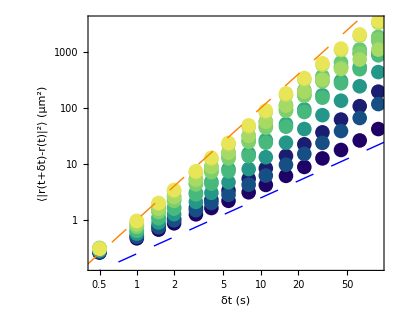

```mathematica
xidxs={1,2,3,8,10,15,17,18,20,22,25,30};
tidxs=Union[Round[10^Range[0,Log10[200],0.15]]];
logxvals=Log[allxvals[[xidxs]]];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
msdplt=Show[ListLogLogPlot[allmsddats[[xidxs,2,tidxs]],
PlotRange->Full,
PlotStyle->cf/@logxvals,
FrameLabel->{"δt (s)",Style["⟨|r(t+δt)-r(t)|^2⟩ (μm^2)",FontSize->20]},
PlotMarkers->ConstantArray[{●,15},6]
],
Plot[{x-1.4,2x},{x,-1,200},PlotStyle->{{Blue,Thick,Dashing[Large]},{Orange,Thick,Dashing[Large]}}]
]
```

```mathematica
Export[figdir<>"/6C_0.3-11.eps",msdplt];
```

### D

#### simulation

```mathematica
ddir=vfdir<>"/motility/lammps_bend/dens_arr/";
mdenss={0,0.01,0.02,0.05,0.1,0.2,0.5,1,2,3,4,5};
ddirs=Flatten[Table[ddir<>"sd"<>ToString[i]<>"e7/dens"<>ToString[NumberForm[md,{2,2}]],{i,5},{md,mdenss}]];
ldir=vfdir<>"/motility/lammps_bend/length_arr/";
nms=Join[Range[2,10],Range[12,26,2]];
ldirs=Flatten[Table[ldir<>"sd"<>ToString[i]<>"e7/nm"<>ToString[nm],{i,5},{nm,nms}]];
kdir=vfdir<>"/motility/lammps_bend/kon_arr/";
ks=Join[Flatten[Outer[Times,10^{-4,-3,-2},{1.,2.,5.}]],0.1Range[10],{2}];
kdirs=Flatten[Table[kdir<>"sd"<>ToString[i]<>"e7/kon"<>If[k<0.01,ToString[NumberForm[k,{2,4}]],ToString[NumberForm[k,{2,2}]]],{i,5},{k,ks}]];
dirs=Join[ddirs,ldirs,kdirs];
maxX=101;
```

```mathematica
actext=ParallelTable[pts3[dir,"actins_ext"],{dir,dirs}];
cms=Map[Mean,actext[[All,All,All,1;;2]],{2}];
cms=MovingAverage[#,20]&/@cms;
lkext=cms[[All,2;;]]-cms[[All,;;-2]];
lps=ParallelTable[plThsq[lkext[[i]],maxX],{i,Length[lkext]}];
```

```mathematica
xvals1=mdenss Lm L0 rd0;
xvals2=(ρ0 Lm(nms-1)) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0));

bnd1=(5Length[mdenss]);
bnd2=bnd1+5Length[nms];
lps1=Mean[Partition[lps[[1;;bnd1]],Length[mdenss]]];
lps2=Mean[Partition[lps[[(bnd1+1);;bnd2]],Length[nms]]];
lps3=Mean[Partition[lps[[(bnd2+1);;]],Length[ks]]];
```

#### theory: duke holy 1995

```mathematica
Lp=17;
kbT=0.004;
visc=0.001;
ka=1;
v0=1;
γ=kbT/visc;
Ls=Range[2,25];
σ0=ρ0;
σx=Sqrt[kbT/ka]^(-5/3)Lp^(-1/3);
σxx=(γ/v0 )^(-5/6)Lp^(-1/3);
davg0=σ0 Lp^(1/5);

ClearAll[davg,savg,pcur,dth,persist];
davg[σ_,σpp_:σxx]:=If[σ>σpp,σ^(-2./5)Lp^(1/5),1/(σ Sqrt[γ/v0])];
savg[l_,d_]:=(l+2d)/(l+3d)(d^2/l)(Exp[l/d]-1-l/d);
pcur[σ_,σpp_:σxx]:=If[σ>σpp,Lp,Lp (σ/σpp)^2];
dth[ρ_,L_]:=3/(ρ L^2);
persist[ρ_,L_,σpp_:σxx]:=1/(1/pcur[ρ,σpp]+dth[ρ,L]^2/savg[L,davg[ρ,σpp]]);

pr={{-1.5,1.5},{-0.8,1.5}};
prplt1=ListPlot[Table[Log10[{ρ0 Lm L rd0,persist[ρ0,L]}],{L,0.01,26,0.01}],PlotStyle->{Red,Thick,Dashed},PlotRange->pr,Joined->True];
prplt2=ListPlot[Table[Log10[{ρ0 Lm L0 rD,persist[ρ0*rD,L0,σxx ]}],{rD,.001/1.01,3/4,0.01}],PlotStyle->{Blue,Thick,Dashed},PlotRange->pr,Joined->True];
prplt3=ListPlot[  
Table[Log10[{ρ Lm L0 rd0,persist[ρ,L0]}],{ρ,0.001,6,0.01}],PlotStyle->{Green,Thick,Dashed},PlotRange->pr,Joined->True];
```

#### plot theory + simulation

```mathematica
xtix=ytix=LogTicks[10,-3,3];
dplt=ListPlot[
Log10[{{xvals1,lps1}ᵀ,{xvals2,lps2}ᵀ,({xvals3,lps3}ᵀ)[[1;;-2]]
}],
Joined->Join[ConstantArray[True,3],ConstantArray[True,6]],
PlotMarkers->Join[ConstantArray[{●,15},3],ConstantArray["·",6]],
PlotStyle->{Green,Red,Blue},
FrameLabel->{"ρ_ml_mLr_D","Path Persistence\nLength (μm)"},
Filling->{4->{5},6->{7},8->{9}},
FrameTicks->{{ytix,Automatic},{xtix,Automatic}},
FillingStyle->Directive[Opacity[0.25],Thickness[0.01]],
PlotRange->pr,
Axes->None];
```

```mathematica
scplt=Show[{dplt,prplt1,prplt2,prplt3}]
```

```mathematica
Export[figdir<>"/6D.eps",scplt]
```

## Figure 7, S3

```mathematica
seeds=10000000Range[20];
dirs=fig7dir<>"/seed"<>ToString[#]&/@seeds;
dir=fig7dir<>"/seed34691004";
```

### A

```mathematica
links=pts[dir,"links"][[1;;-2]];
ams=pts[dir,"amotors"][[1;;-2]];
pms=pts[dir,"pmotors"][[1;;-2]];
idxs={1,21,51,199};
frs=draw[{},links[[idxs]],ams[[idxs,1;;-1;;2]],pms[[idxs,1;;-1;;10]],dir,False,{50,50},1,False,16];
GraphicsRow[frs,ImageSize->1000]
```

```mathematica
Export[figdir<>"/7A.eps",GraphicsRow[frs,ImageSize->1000]];
```

### B

```mathematica
nm=11;
nparts=500*nm;
rngs=Table[Join[Range[1,nm i],Range[nm(i+1)+1,nparts]],{i,0,nparts/nm-1}];
(*All pairs of actin beads that are not on the same filament*)
allPairs=Union[Sort/@Flatten[
Table[{i,j},
{i,nparts},
{j,RandomSample[rngs[[Quotient[i-1,nm]+1]],1000]}],1]];
(*A sample of them*)
sampPairs=RandomSample[allPairs,500*499/2];
idxs={1,21,51,101,200};
acts=pts[dir,"actins"];
gr=rdf[acts[[idxs]],{50,50},0.05,5,sampPairs];
cf=ColorData[{"BlueGreenYellow",Log10[{1,400}]}];
ts=2(idxs-1);
```

```mathematica
grplot=ListPlot[gr,PlotStyle->Table[{cf[Log10[t+1]],Thick},{t,ts}],FrameLabel->{"distance (μm)","radial distr. func."},Joined->True,PlotRange->Full,PlotLegends->Placed[SwatchLegend[ts,LegendLabel->"time (s)",LegendMarkerSize->20,Spacings->0,LegendLayout->"ReversedColumn"],{0.8,0.65}],DataRange->{0.025,4.975}]
```

```mathematica
Export[figdir<>"/7B.eps",grplot];
```

### C

C,D, and S4 require you to have run the Python divergence calculating code "div_by_vbin.py" available in the versatile_framework _paper directory, and described in section S4 of the paper. The command to run is
python div_by_vbin.py [fig7dir]
there are lots of parameters you can toy with, to see them enter
python div_by_vbin.py --help
For the rest of the figures I used the output with the default parameter choices: 
fov = [50,50]
rbfunc = ‘gaussian’
rbeps = 5
dr = [1,1]
dt = 10
padding = 1
nbins = 10
minpts = 10
div_lsc = 10

```mathematica
vf40=Import[dir<>"/analysis/xyuvd_nbins10_lsc10/t20.txt","TABLE"];
xyuv={vf40[[All,1;;2]],vf40[[All,3;;4]]}ᵀ;
xyd=vf40[[All,{1,2,5}]];
xyd=#/{1,1,2}&/@xyd;(*because of 2s timestep*)
ldp=ListDensityPlot[xyd,PlotRange->25{{-1,1},{-1,1}},
ColorFunction->ColorData[{"ThermometerColors",{0.025,-0.025}}],ColorFunctionScaling->False,InterpolationOrder->1,FrameTicksStyle->White];
lvp=ListVectorPlot[xyuv,PlotRange->25{{-1,1},{-1,1}},Background->None];
mylvpd=Overlay[{ldp,lvp}]
```

```mathematica
Export[figdir<>"/7C.png",mylvpd];
```

### D & S3

#### Calculate Divergence at some small discretization

```mathematica
fov=50;
dr=1;
dt=10;
tf=400;

edgex=Range[-fov/2,fov/2,dr];
edgey=edgex;
dx=dr;dy=dr;
xbins=0.5(edgex[[2;;]]+edgex[[;;-2]]);
ybins=0.5(edgey[[2;;]]+edgey[[;;-2]]);
bins=Table[{x,y},{x,xbins},{y,ybins}];
```

```mathematica
vfs=ParallelTable[Import[dr<>"/analysis/vfield_weights_nbins10_lsc10_dt"<>ToString[dt]<>"_thresh10/t"<>ToString[t]<>".txt","TABLE"],{dr,dirs},{t,Range[0,tf-dt-1]}];
ClearAll[mydivs];
mydivs=Table[With[{vf=vfs[[i,t]]},div[#[[1]],#[[2]],vf]&],{i,Length[vfs]},{t,Length[vfs[[i]]]}];
```

$Aborted

```mathematica
ParallelDo[
Export[dirs[[i]]<>"/analysis/div_dr"<>ToString[dr]<>"/t"<>ToString[t]<>".dat",Map[mydivs[[i,t]],bins,{2}]],
{i,Length[dirs]},{t,Length[mydivs[[i]]]}];
```

#### Calculate bincount at same discretization

```mathematica
bincts=ParallelDo[
acts=pts[dir,"actins"];
bcs=Table[BinCounts[acts[[t,All,1;;2]],{-fov/2,fov/2,dr},{-fov/2,fov/2,dr}],{t,Length[acts]}];
Export[dir<>"/analysis/bin_counts_dr"<>ToString[dr]<>".dat",bcs],
{dir,dirs}
];
```

### D

```mathematica
(*If the density calculation doesn't exist yet*)
acts=ParallelTable[pts[dr,"actins"],{dr,dirs}];
bcs=Table[BinCounts[acts[[i,t,All,1;;2]],{-fov/2,fov/2,dr},{-fov/2,fov/2,dr}],
{i,Length[acts]},{t,Length[acts[[i]]]}
];
Export[vfdir<>"/contracting/xldens1/bincounts_all.dat",bcs];
```

```mathematica
(*If the filament strain calculation doesn't exist yet*)
strs=ParallelMap[filstrain,acts];
Export[vfdir<>"/contracting/xldens1/strains_all.dat",strs];
```

```mathematica
(*If they all do exist*)
strs=ToExpression[Import[vfdir<>"/contracting/xldens1/strains_all.dat","TSV"]];
bcs=Table[ToExpression[Import[dr<>"/analysis/bin_counts_dr1_dt10.dat","TSV"]],{dr,dirs}];
```

```mathematica
dr=5;
bcsdr=Table[Map[Total[Flatten[#]]&,Partition[bcs[[i,t]],{dr,dr}],{2}],{i,Length[bcs]},{t,Length[bcs[[i]]]}];
divs=Table[Import[dir<>"/analysis/div_dr1_dt"<>ToString[dt]<>"/t"<>ToString[t]<>".dat","Table"],{dir,dirs},{t,tf-dt}];
divsdr=Table[Map[Total[Flatten[#]]&,Partition[divs[[i,t]],{dr,dr}],{2}],{i,Length[divs]},{t,Length[divs[[i]]]}];
```

```mathematica
rhodivs=Table[Total[bcsdr[[i,t]]*divsdr[[i,t]]/dr^2,2],{i,Length[divsdr]},{t,Length[divsdr[[i]]]}];
meandiv=Mean[rhodivs];
errdiv=StandardDeviation[rhodivs]/Sqrt[Length[seeds]];
meanstr=Mean[strs];
errstr=StandardDeviation[strs]/Sqrt[Length[seeds]];
```

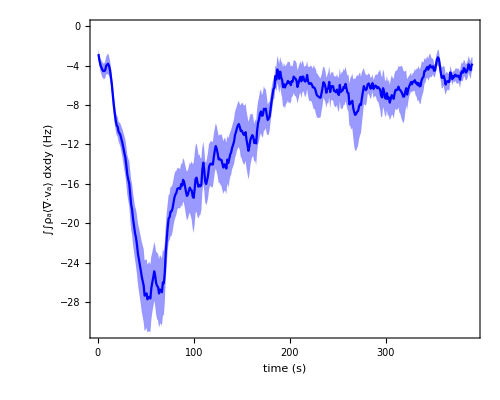
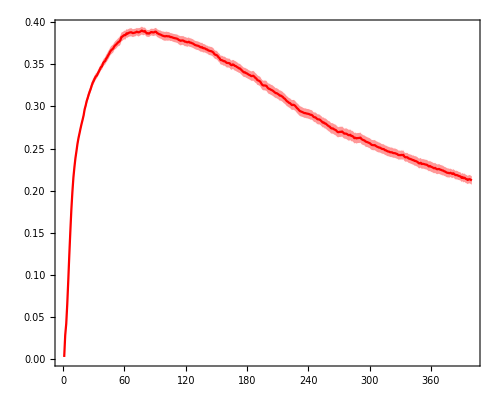

```mathematica
lp1=ListPlot[{meandiv,meandiv-errdiv,meandiv+errdiv},
Joined->True,
PlotStyle->{Blue,{Blue,Opacity[0.01]},{Blue,Opacity[0.01]}},
Filling->{2->{3}},
FillingStyle->Opacity[0.4],
PlotRange->{-31,0},
FrameStyle->{{Blue,Black},{Black,Black}},
FrameTicks->{{Automatic,Automatic},{LinTicks[0,400,100,10],Automatic}},
FrameLabel->{"time (s)","∫∫ρ_a⟨∇·v_a⟩ dxdy  (Hz)"},
ImagePadding->100,
ImageSize->500];
lp2=ListPlot[{meanstr,meanstr-errstr,meanstr+errstr},
Joined->True,PlotRange->Full,
PlotStyle->{Red,{Red,Opacity[0.01]},{Red,Opacity[0.01]}},
Filling->{2->{3}},
FillingStyle->Opacity[0.4],
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Red,Red},{Black,Black}},
FrameLabel->{"","filament strain","",""},
ImagePadding->100,
ImageSize->500];
divstrplt=Overlay[
{Show[lp1,Frame->{{True,False},{True,True}}],
Show[lp2,Frame->{{False,True},{False,False}},
FrameTicks->All,
FrameLabel->{"","","",Rotate["filament strain",Pi]}]}]
```

```mathematica
Export[figdir<>"/7D.png",divstrplt];
```

### S3

```mathematica
t=60;
```

#### A (frame)

```mathematica
links=pts[dirs[[1]],"links"][[t]];
ams=pts[dirs[[1]],"amotors"][[t]];
pms=pts[dirs[[1]],"pmotors"][[t]];
```

```mathematica
fr=draw[{},{links},{ams[[1;;-1;;2]]},{pms[[1;;-1;;10]]},dir,False,{50,50},1,False,16];
Show[fr]
```

```mathematica
Export[figdir<>"/S4A_left.eps",Show[fr,ImageSize->1000]];
```

#### A (Unweighted)

```mathematica
ClearAll[wft,uft,vft,divft];
wft=Import[dirs[[1]]<>"/analysis/vfield_weights_nbins10_lsc10_dt10_thresh10/t"<>ToString[t]<>".txt","TABLE"];
uft[i_,j_]:=velx[i,j,wft];
vft[i_,j_]:=vely[i,j,wft];
divft[i_,j_]:=div[i,j,wft];
```

```mathematica
dplt=DensityPlot[divft[x,y],{x,-25,25},{y,-25,25},PlotRange->{25{-1,1},25{-1,1},All},
ColorFunction->ColorData[{"ThermometerColors",0.1{1,-1}}],ColorFunctionScaling->False,FrameTicksStyle->White];
vplt=VectorPlot[{uft[x,y],vft[x,y]},{x,-25,25},{y,-25,25},PlotRange->25{{-1,1},{-1,1}},Background->None];
```

```mathematica
Overlay[{dplt,vplt}]
```

```mathematica
Export[figdir<>"/S4A_middle.png",Overlay[{dplt,vplt}]];
```

#### A (Weighted by density)

```mathematica
dr=1;
dt=10;
divt=Import[dirs[[1]]<>"/analysis/div_dr"<>ToString[dr]<>"_dt"<>ToString[dt]<>"/t"<>ToString[t]<>".dat","Table"];
bct=ToExpression[Import[dirs[[1]]<>"/analysis/bin_counts_dr"<>ToString[dr]<>"_dt"<>ToString[dt]<>".dat","TSV"]][[t]];
xs=ys=Range[-fov/2+0.5,fov/2-0.5,1];
dat=Flatten[Table[{xs[[i]],ys[[j]],divt[[i,j]]*bct[[i,j]]},{i,Length[xs]},{j,Length[ys]}],1];
dplt2=ListDensityPlot[dat,PlotRange->{25{-1,1},25{-1,1},All},
ColorFunction->ColorData[{"ThermometerColors",0.1{1,-1}}],ColorFunctionScaling->False,FrameTicksStyle->White,InterpolationOrder->0];
```

```mathematica
Export[figdir<>"/S4A_right.png",Overlay[{dplt2,vplt}]];
```

#### B

```mathematica
fov=50;tf=400;dt=10;
drs={1,2,5,10,25,50};
```

```mathematica
bcs=Table[ToExpression[Import[dr<>"/analysis/bin_counts_dr1_dt10.dat","TSV"]],{dr,dirs}];
divs=Table[Import[dir<>"/analysis/div_dr1_dt"<>ToString[dt]<>"/t"<>ToString[t]<>".dat","Table"],{dir,dirs},{t,tf-dt}];
```

```mathematica
bcsdr=Table[Map[Total[Flatten[#]]&,Partition[bcs[[i,t]],{dr,dr}],{2}],{dr,drs},{i,Length[bcs]},{t,Length[bcs[[i]]]}];
divsdr=Table[Map[Total[Flatten[#]]&,Partition[divs[[i,t]],{dr,dr}],{2}],{dr,drs},{i,Length[divs]},{t,Length[divs[[i]]]}];
rhodivs=Table[Total[bcsdr[[i,j,t]]*divsdr[[i,j,t]]/drs[[i]]^2,2],{i,Length[divsdr]},{j,Length[divsdr[[i]]]},{t,Length[divsdr[[i,j]]]}];
meandiv=Mean/@rhodivs;
```

```mathematica
divdrplt=ListPlot[meandiv,
PlotStyle->"BlueGreenYellow",
Joined->True,
PlotRange->{{-10,395},{-36,4}},
FrameLabel->{"time (s)","∫∫ρ_a⟨∇·v_a⟩ dxdy  (Hz)"},
PlotLegends->Placed[SwatchLegend[drs,Spacings->0,LegendLayout->"ReversedColumn",LegendMarkerSize->15,LabelStyle->FontSize->17,LegendLabel->Placed[Rotate["dx and dy (μm)",Pi/2],Left]],{0.86,0.33}]]
```

```mathematica
Export[figdir<>"/S4B_new.eps",divdrplt];
```

#### C

```mathematica
dts={1,2,5,10,20};
fov=50;tf=400;

dr=1;
edgex=Range[-fov/2,fov/2,dr];
edgey=edgex;
dx=dr;dy=dr;
xbins=0.5(edgex[[2;;]]+edgex[[;;-2]]);
ybins=0.5(edgey[[2;;]]+edgey[[;;-2]]);
bins=Table[{x,y},{x,xbins},{y,ybins}];
```

```mathematica
ParallelDo[
vf=Import[dir<>"/analysis/vfield_weights_nbins10_lsc10_dt"<>ToString[dt]<>"_thresh10/t"<>ToString[t]<>".txt","TABLE"];
divdr1=Map[div[#[[1]],#[[2]],vf]&,bins,{2}];
Export[dir<>"/analysis/div_dr"<>ToString[dr]<>"_dt"<>ToString[dt]<>"/t"<>ToString[t]<>".dat",divdr1],
{dt,dts[[{1,2,3,5}]]},
{dir,dirs},
{t,tf-dt-1}];
```

```mathematica
bcs=Table[ToExpression[Import[dr<>"/analysis/bin_counts_dr1.dat","TSV"]],{dr,dirs}];
dr=5;
bcsdr=Table[Map[Total[Flatten[#]]&,Partition[bcs[[i,t]],{dr,dr}],{2}],{i,Length[bcs]},{t,Length[bcs[[i]]]}];
bcsdt=Table[MovingAverage[bcsdr[[i]],dt],{dt,dts},{i,Length[bcsdr]}];
bcsdt=0.5(bcsdt[[All,All,2;;]]+bcsdt[[All,All,;;-2]]);
```

```mathematica
dr=5;
divsdt=ParallelTable[
Map[Total[Flatten[#]]&,
Partition[
Import[dir<>"/analysis/div_dr1_dt"<>ToString[dt]<>"/t"<>ToString[t]<>".dat","Table"],
{dr,dr}],{2}],
{dt,dts},{dir,dirs},{t,tf-dt-1}];
```

```mathematica
rhodivs=Table[1/25Total[bcsdt[[i,j,t]]*divsdt[[i,j,t]],2],{i,Length[divsdt]},{j,Length[divsdt[[i]]]},{t,Length[divsdt[[i,j]]]}];
meandiv=Mean/@rhodivs;
```

```mathematica
divdtplt=ListPlot[meandiv,
PlotStyle->"BlueGreenYellow",
Joined->True,
PlotRange->{{-10,395},{-36,4}},
FrameLabel->{"time (s)","∫∫ρ_a⟨∇·v_a⟩ dxdy  (Hz)"},
PlotLegends->Placed[SwatchLegend[dts,Spacings->0,LegendLayout->"ReversedColumn",LegendMarkerSize->15,LabelStyle->FontSize->17,LegendLabel->Placed["h (sec)",Bottom]],{0.8,0.25}]]
```

```mathematica
Export[figdir<>"/S4C_new_h.eps",divdtplt];
```

## S4

```mathematica
dx=1;
L=20;
nfils=20;
nlks=L/dx;
nacts=nlks+1;
teq=1000;
lppred=17;
xs=Range[dx,L-dx,dx];
maxl=5;
```

### A

```mathematica
figS4Adir=figS4dir<>"/fiber20/seg1.00";
acts=Partition[#,nacts]&/@ptsCS[figS4Adir,"objects"];
lks=acts[[All,All,2;;]]-acts[[All,All,;;-2]];

angs=ParallelMap[anglesTCS,lks,{2}];
angsbw=ParallelMap[anglesBwT,angs,{2}];

th2s=ParallelMap[th2,angsbw,{2}];
muths=Mean[th2s[[teq;;]]];
muthsmu=Mean[muths];
muthserr=StandardDeviation[muths]/Sqrt[nfils];

ccfs=ParallelMap[ccf,angsbw,{2}];
muccfs=Mean[ccfs[[teq;;-1]]];
muccfsmu=Mean[muccfs];
muccferr=StandardDeviation[muccfs]/Sqrt[nfils];
```

```mathematica
th2plt=Show[
ListPlot[{
{xs,muthsmu}ᵀ,
{xs,muthsmu-muthserr}ᵀ,
{xs,muthsmu+muthserr}ᵀ},
FrameLabel->{"","","",Rotate[Style["⟨θ^2(ℓ)⟩",Blue],Pi]},
FrameStyle->Blue,
Frame->{{False,True},{False,False}},
FrameTicks->{{None,All},{None,None}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Blue,{Blue,Opacity[0.01]},{Blue,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},*)
(**)
(*Uncomment next four line if you don't want joined*)

FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Blue,
Joined->False,

Filling->{2->{3}},
PlotRange->{{0,20},Automatic}
],
Plot[{x/(lp)},{x,0,50},PlotStyle->{Thick,Dashing[Large],Blue}]
];
```

```mathematica
ccfplt=Show[
ListLogPlot[{
{xs,muccfsmu}ᵀ,
{xs,muccfsmu-muccferr}ᵀ,
{xs,muccfsmu+muccferr}ᵀ},
FrameLabel->{"ℓ (μm)",Style["⟨cosθ(ℓ)⟩",Red]},
FrameStyle->{{Red,Automatic},{Black,Black}},
Frame->{{True,False},{True,True}},
FrameTicks->{{All,None},{All,Automatic}},
(*Comment out next three lines if you don't want joined*)
(**)
(*PlotStyle->{Red,{Red,Opacity[0.01]},{Red,Opacity[0.01]}},
PlotMarkers->{{●,10},{○,0.01},{○,0.01},{●,5},{○,0.01},{○,0.01}},
Joined->{False,True,True},*)
(**)
(*Uncomment next four line if you don't want joined*)
(**)
FillingStyle->Directive[Opacity[1],Thickness[0.003]],
PlotMarkers->{{●,12},"+","+"},
PlotStyle->Red,
Joined->False,
(**)
Filling->{2->{3}},
PlotRange->{{0,20},Automatic}],
LogPlot[{Exp[-x/(2lp)]},{x,0,50},PlotStyle->{Thick,Dashing[Large],Red}]
];
```

```mathematica
{ccfplt,th2plt}
```

```mathematica
Export[figdir<>"/S4A_red.eps",ccfplt];
Export[figdir<>"/S4A_blue.eps",th2plt];
```

### B

```mathematica
kbdir=figS4dir<>"/fiber20_seg1";
kbs={0.005,0.01,0.02,0.05,0.1,0.2,0.5,1.0,2.0,5,10,20,50,100,200,500};
kbdirs=kbdir<>"/kb"<>ToString[NumberForm[#,{1,3},ExponentFunction->(Null&)]]&/@kbs;
```

```mathematica
acts=Table[Partition[#,nacts]&/@ptsCS[dir,"objects"],{dir,kbdirs}];
lks=acts[[All,All,All,2;;]]-acts[[All,All,All,;;-2]];
lps=Table[plMeanThsq[lks[[i,All,j]],dx,L,maxl],{i,Length[lks]},{j,Length[lks[[i,1]]]}];
lpmeans=Mean/@lps;
```

```mathematica
lplpplt=Show[
ListLogLogPlot[
{{kbs/0.004,lpmeans}ᵀ(*,
{kbs[[3;;]]/0.004,1/msmidkb[[3;;]]}ᵀ*)
},
PlotMarkers->{●,15},
PlotStyle->{Red,{Blue,Opacity[0.75]}},
Joined->False
],
LogLogPlot[x,{x,0.1,500000},PlotStyle->{Black,Dashing[0.02](*,Thick*)}],
FrameLabel->{"κ_B (k_BT×μm)","L_p(μm)"}];
```

```mathematica
lplpplt
```

```mathematica
Export[figdir<>"/S4B.eps",lplpplt];
```

### C

```mathematica
dxdir=figS4dir<>"/fiber20_dt5e-4/";
dxs={0.08,0.1,0.2,0.25,0.4,0.5,0.8,1,2,2.5,4};
dxdirs=dxdir<>"/seg"<>ToString[NumberForm[#,{2,2},ExponentFunction->(Null&)]]&/@dxs;
nacts=L/dxs+1;
acts=ptsCS[#,"objects"]&/@dxdirs;
actsp=Table[Partition[#,Round[nacts[[i]]]]&/@acts[[i]],{i,Length[nacts]}];
lks=actsp[[All,All,All,2;;]]-actsp[[All,All,All,;;-2]];
lps=Table[plMeanThsq[lks[[i,All,j]],dxs[[i]],L,maxl],{i,Length[lks]},{j,Length[lks[[i,1]]]}];
lpmeans=Mean/@lps;
lperrs=(StandardDeviation/@lps)/Sqrt[nfils];
```

```mathematica
dxlpplt=Show[
ListLogLinearPlot[
{{dxs,lpmeans}ᵀ,
{dxs,lpmeans-lperrs}ᵀ,
{dxs,lpmeans+lperrs}ᵀ
(*,{dxs,lpmeans}ᵀ,
{dxs,lpmeans-lperrs}ᵀ,
{dxs,lpmeans+lperrs}ᵀ,*)
},
PlotMarkers->{{●,15},{"·",0},{"·",0},{●,15},{"·",0},{"·",0}},
PlotStyle->{Red,Red,Red(*Blue,Blue,Blue,*)},
Joined->False,
Filling->{2->{3}},(*{{2->{3}},{5->{6}}},*)
FillingStyle->Directive[Opacity[1],Thickness[0.01]],
PlotRange->Full,
PlotLegends->Placed[SwatchLegend[{{"CytoSim",None,None,"AFiNeS"},{Red,Blue}},LegendMarkers->{●,15},LegendFunction->Framed,LabelStyle->FontSize->20],{0.5,0.75}]
],
LogLinearPlot[lppred,{x,0.001,10000},PlotStyle->{Black,Dashing[0.02]}],
FrameLabel->{"l_a (μm)","L_p(μm)"}];
```

```mathematica
Export[figdir<>"/S4C.eps",lplpplt];
```

## S5

```mathematica
rd0=0.5;
ρ0=4;
L0=15;
Lm=0.5;
koff0=1;
```

### A

```mathematica
dir=figS5dir<>"/kon";
ks=Join[Flatten[Outer[Times,{0.001,0.01,0.1,1},{1,2,5}]],{10,20}];
dirs=dir<>ToString[NumberForm[#,{2,3}]]&/@ks;
konarr=ptsCS[#,"objects"]&/@dirs;
konarr=ParallelMap[rijP[#,{50,50}]&,konarr,{3}];
konarr=Map[Join[#,{0.5}]&,konarr,{3}];
maxf=401;
cf=ColorData[{"DeepSeaColors",{1,maxf}}];
cf2[i_]:=Blend[{Pink,Darker[Red]},(i-1)/(maxf-1)];
start=5;
fs=Table[
draw[
konarr[[j,{i+start}]],{},{},{},dirs[[-1]],False,25{{-1,1},{-1,1}},1,True,16,cf2[i]
],
{j,1,Length[konarr]},
{i,1,maxf,40}
];
pics=Show/@fs;
grow=GraphicsRow[pics[[{4,6,7,10}]],Spacings->20];
grow
```

```mathematica
Export[figdir<>"/S5A.eps",grow];
```

### B

#### Green

```mathematica
dir1=figS5dir<>"/nmyo";
ρs=Join[{25,50,125},250Range[10],2500Range[10]];
dirs=dir1<>ToString[Round[#]]&/@ρs;
acts1=Table[ptsCS[dr,"objects"],{dr,dirs}];
```

```mathematica
lks1=acts1[[All,All,2;;]]-acts1[[All,All,;;-2]];
cms1=0.5(acts1[[All,All,;;-2]]+acts1[[All,All,2;;]]);
drps1=cms1[[All,2;;]]-cms1[[All,;;-2]];
(*drps1=Map[rijP[#,{50,50}]&,drs,{3}];*)
vs=Map[Norm[#]&,drps1,{3}];
norms=Map[Norm,lks1[[All,1;;-2]],{3}];
rspar=lks1[[All,1;;-2]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];

vspar=MapThread[Dot,{drps1,rspar},3];
vsperp=MapThread[Dot,{drps1,rsperp},3];

dt=0.5;
muvs=Mean/@Flatten/@vs/dt;
par1=Mean/@Flatten/@vspar/dt;
perp1=Sqrt[-par1^2+muvs^2];
```

#### Red Curve

```mathematica
dir2=figS5dir<>"/len";
nms=Range[2,25];
dirs=dir2<>ToString[#]&/@nms;
acts2=Table[ptsCS[dr,"objects"],{dr,dirs}];
```

```mathematica
lks2=acts2[[All,All,2;;]]-acts2[[All,All,;;-2]];
cms2=0.5(acts2[[All,All,;;-2]]+acts2[[All,All,2;;]]);
drps2=cms2[[All,2;;]]-cms2[[All,;;-2]];
vs=Map[Norm[#]&,drps2,{3}];
norms=Map[Norm,lks2[[All,1;;-2]],{3}];
rspar=lks2[[All,1;;-2]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];
vspar=Table[drps2[[i,j,k]].rspar[[i,j,k]],{i,Length[drps2]},{j,Length[drps2[[i]]]},{k,Length[drps2[[i,j]]]}];
vsperp=Table[drps2[[i,j,k]].rsperp[[i,j,k]],{i,Length[drps2]},{j,Length[drps2[[i]]]},{k,Length[drps2[[i,j]]]}];

dt=0.5;
muvs=Mean/@Flatten/@vs/dt;
par2=Mean/@Flatten/@vspar/dt;
perp2=Sqrt[-par2^2+muvs^2];
```

#### Blue Curve

```mathematica
dir=figS5dir<>"/kon";
ks=Join[Flatten[Outer[Times,{0.001,0.01,0.1,1},{1,2,5}]],{10,20}];
dirs=dir<>ToString[NumberForm[#,{1,3}]]&/@ks;
acts3=Table[ptsCS[dr,"objects"],{dr,dirs}];

lks3=acts3[[All,All,2;;]]-acts3[[All,All,;;-2]];
cms3=0.5(acts3[[All,All,;;-2]]+acts3[[All,All,2;;]]);
drps3=cms3[[All,2;;]]-cms3[[All,;;-2]];
vs=Map[Norm[#]&,drps3,{3}];
norms=Map[Norm,lks3[[All,1;;-2]],{3}];
rspar=lks3[[All,1;;-2]]/norms;
rsperp=Table[{-rspar[[i,j,k,2]],rspar[[i,j,k,1]]},{i,Length[rspar]},{j,Length[rspar[[i]]]},{k,Length[rspar[[i,j]]]}];



vspar=Table[drps3[[i,j,k]].rspar[[i,j,k]],{i,Length[drps3]},{j,Length[drps3[[i]]]},{k,Length[drps3[[i,j]]]}];
vsperp=Table[drps3[[i,j,k]].rsperp[[i,j,k]],{i,Length[drps3]},{j,Length[drps3[[i]]]},{k,Length[drps3[[i,j]]]}];

dt=0.5;
muvs=Mean/@Flatten/@vs/dt;
par3=Mean/@Flatten/@vspar/dt;
perp3=Sqrt[-par3^2+muvs^2];
```

#### Whole Plot

```mathematica
rd0=0.5;
ρ0=4;
L0=15;
Lm=0.5;
koff0=1;
```

```mathematica
xvals1=ρs/2500 Lm L0 rd0;
xvals2=(ρ0 Lm(nms-1)) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0));
```

```mathematica
headers=Map[Style[#,FontSize->22,FontFamily->"Arial"]&,{{"ρ","L","r_D"},{"v_(||)","v_⊥"}},{2}];
legtable[pairs_]:=TableForm[
Partition[pairs,3]ᵀ,TableAlignments->Left,TableSpacing->{1,1},
TableHeadings->headers,Frame->True];
sz=10;
tab=
{{"","v_(||)","v_⊥"},
{"ρ_m",Graphics[{Green,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->sz]},
{"L",Graphics[{Red,Disk[{0,0},0.1]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Red]],White,Rectangle[]},ImageSize->sz]},
{"r_D",Graphics[{Blue,Disk[]},ImageSize->sz],Graphics[{EdgeForm[Directive[Thick,Blue]],White,Rectangle[]},ImageSize->sz]}};
leg=Grid[tab,BaseStyle->{FontSize->19,FontFamily->"Arial"},Frame->All,Spacings->{0.2,0.2},Background->{{LightGray,None},{LightGray,None}}];
```

```mathematica
vplt1=ListPlot[
{{xvals1,-par1}ᵀ,{xvals2,-par2}ᵀ,{xvals3,-par3}ᵀ,
{xvals1,perp1}ᵀ,{xvals2,perp2}ᵀ,{xvals3,perp3}ᵀ},Joined->True,
PlotMarkers->{{●,10},{●,10},{●,10},{□,15},{□,15},{□,15}},
PlotStyle->{Green,Red,Blue,Green,Red,Blue},PlotRange->{{0,30},{0.3,1.5}},
FrameLabel->{"ρ_ml_mLr_D","v(μm/s)"}];
```

```mathematica
vplt=Overlay[{vplt1,leg},Alignment->{0.6,0.8}]
```

```mathematica
Export[figdir<>"/S5B.eps",vplt];
```

### C (Continued from B)

```mathematica
ms1=Table[msdpc[drps1[[j,All,i]]],{j,1,Length[drps1]},{i,1,L0}];
ms2=Table[msdpc[drps2[[j,All,i]]],{j,1,Length[drps2]},{i,1,nms[[j]]-1}];
ms3=Table[msdpc[drps3[[j,All,i]]],{j,1,Length[drps3]},{i,1,L0}];
```

```mathematica
(*Sort MSD data sets by their xval*)
msddats1=Table[{xvals1[[i]],{Range[1999]*dt,Mean[ms1[[i]]]}ᵀ},{i,1,Length[ms1]}];
msddats2=Table[{xvals2[[i]],{Range[1999]*dt,Mean[ms2[[i]]]}ᵀ},{i,1,Length[ms2]}];
msddats3=Table[{xvals3[[i]],{Range[1999]*dt,Mean[ms3[[i]]]}ᵀ},{i,1,Length[ms3]}];
allmsddats=Sort[Join[msddats1,msddats2,msddats3]];
allxvals=allmsddats[[All,1]];
```

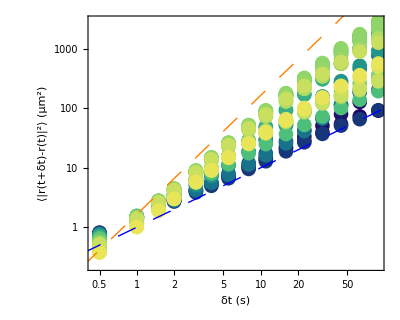

```mathematica
xidxs=Range[29];
tidxs=Union[Round[10^Range[0,Log10[200],0.15]]];
logxvals=Log[allxvals[[xidxs]]];
cf=ColorData[{"BlueGreenYellow",{Min[logxvals],Max[logxvals]}}];
msdplt=Show[ListLogLogPlot[allmsddats[[xidxs,2,tidxs]],
PlotRange->Full,
PlotStyle->cf/@logxvals,
(*PlotStyle->(ColorData[{"BlueGreenYellow",Log[{allxvals[[1]],allxvals[[maxidx]]}]}][#]&/@Log[allxvals[[1;;maxidx;;didx]]]),*)
FrameLabel->{"δt (s)",Style["⟨|r(t+δt)-r(t)|^2⟩ (μm^2)",FontSize->20]},
PlotMarkers->ConstantArray[{●,15},6]
],
Plot[{x,2x+0.5},{x,-1,200},PlotStyle->{{Blue,Thick,Dashing[Large]},{Orange,Thick,Dashing[Large]}}]
]
```

```mathematica
Export[figdir<>"/S5C.eps",msdplt];
```

### D

```mathematica
ddir=figS5dir<>"/dens_arr/";
mdenss={0.01,0.02,0.05,0.1,0.2,0.5,1,2,3,4,5};
ddirs=Flatten[Table[ddir<>"sd"<>ToString[i]<>"000000/nmyo"<>ToString[Round[md*2500]],{i,5},{md,mdenss}]];
ldir=figS5dir<>"/len_arr/";
ls=Join[Range[1,9],Range[11,25,2]];
ldirs=Flatten[Table[ldir<>"sd"<>ToString[i]<>"000000/len"<>ToString[l],{i,5},{l,ls}]];
kdir=figS5dir<>"/kon_arr/";
ks=Flatten[Outer[Times,10^{-3,-2,-1,0},{1.,2.,5.}]];
kdirs=Flatten[Table[kdir<>"sd"<>ToString[i]<>"000000/kon"<>ToString[NumberForm[k,{2,3}]],{i,5},{k,ks}]];
dirs=Join[ddirs,ldirs,kdirs];
maxX=101;
```

```mathematica
acts=ParallelTable[ptsCS[dir,"objects"],{dir,dirs}];
cms=Map[Mean,acts[[All,All,All,1;;2]],{2}];
cms=MovingAverage[#,20]&/@cms;
lkext=cms[[All,2;;]]-cms[[All,;;-2]];
lps=ParallelTable[plThsq[lkext[[i]],maxX],{i,Length[lkext]}];
```

```mathematica
xvals1=mdenss Lm L0 rd0;
xvals2=(ρ0 Lm ls) rd0;
xvals3=(ρ0 Lm L0)(ks/(ks+koff0));
bnd1=(5Length[mdenss]);
bnd2=bnd1+5Length[ls];
lps1=Mean[Partition[lps[[1;;bnd1]],Length[mdenss]]];
lps2=Mean[Partition[lps[[(bnd1+1);;bnd2]],Length[ls]]];
lps3=Mean[Partition[lps[[(bnd2+1);;]],Length[ks]]];
```

```mathematica
xtix=LogTicks[10,-3,2];
ytix=LogTicks[10,-3,2];
pr={{-1.5,1.5},{-0.8,1.5}};
dplt=ListPlot[
Log10[{{xvals1,lps1}ᵀ,{xvals2,lps2}ᵀ,({xvals3,lps3}ᵀ)[[1;;-2]]
}],
Joined->Join[ConstantArray[True,3],ConstantArray[True,6]],
PlotMarkers->Join[ConstantArray[{●,15},3],ConstantArray["·",6]],
PlotStyle->{Green,Red,Blue},
FrameLabel->{"ρ_ml_mLr_D","Path Persistence\nLength (μm)"},
Filling->{4->{5},6->{7},8->{9}},
FrameTicks->{{ytix,Automatic},{xtix,Automatic}},
FillingStyle->Directive[Opacity[0.25],Thickness[0.01]],
PlotRange->pr,
Axes->None];
```

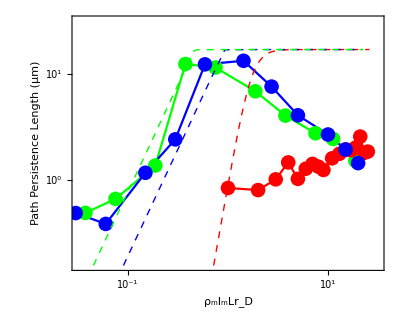

```mathematica
scplt=Show[{dplt,prplt1,prplt2,prplt3}] (*The "prplt"s should have been computed above, in Fig6*)
```

```mathematica
Export[figdir<>"/S5D.eps",scplt];
```